```mathematica
Piecewise
```

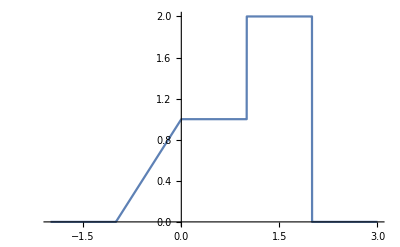

```mathematica
Plot[Piecewise[{{x+1,-1<x<0},{1,0<x<1},{2,1<x<2}}],{x,-2,3},Exclusions->None]
```

```mathematica
f[x_]:=Piecewise[{{x+1,-1<x<0},{1,0<x<1},{2,1<x<2}}]
```

```mathematica
g[x_,t_]:=1/(√(2π t))Exp[-1/(2t)x^2]
```

```mathematica
uu[y_,t_]=Convolve[f[x],g[x,t],x,y]
```

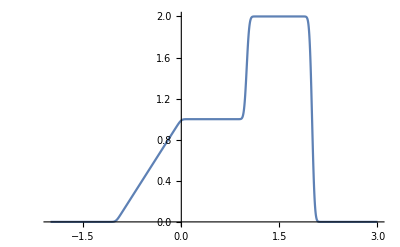

```mathematica
Plot[uu[y,.001],{y,-2,3}]
```

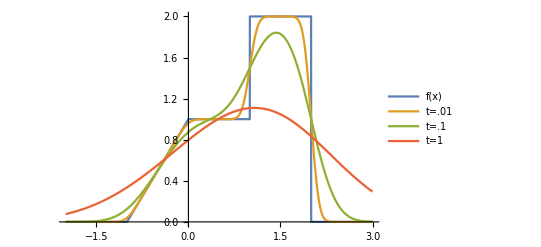

```mathematica
Plot[{f[x],uu[x,.01],uu[x,.1],uu[x,1]},{x,-2,3},PlotLegends->Placed[{"f(x)","t=.01","t=.1","t=1"},Right],Exclusions->None]
```

```mathematica
D[G[s-x,t],{x,1}]
```

-G^(1,0)[s-x,t]

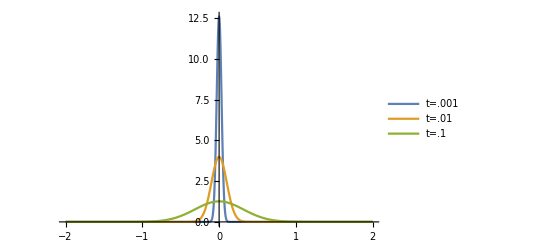

```mathematica
Plot[{12.6156626101008 ⅇ^(-500. x^2),3.989422804014327 ⅇ^(-50. x^2),1.2615662610100802 ⅇ^(-5. x^2)},{x,-2,2},PlotLegends->{"t=.001","t=.01","t=.1"},PlotRange->Full]
```

```mathematica
Table[g[x,t],{t,{.001,.01,.1}}]
```

{12.6157 ⅇ^(-500. x^2),3.98942 ⅇ^(-50. x^2),1.26157 ⅇ^(-5. x^2)}

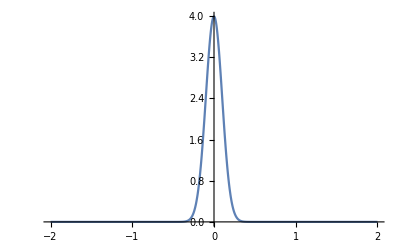

```mathematica
Plot[3.989422804014327 ⅇ^(-50. x^2),{x,-2,2},PlotRange->Full]
```